# 問題 3.3 について

## 準備

### 同次座標から直交座標へ変換する命令の定義

```mathematica
HomToOrth3D[list_]:={list[[1]]/list[[4]],list[[2]]/list[[4]],list[[3]]/list[[4]]}
```

### 視点が V(10, 3, 1/2) ，投影面が x=0 の透視投影を表す4次正方行列

```mathematica
HomToOrth3D[{20,6,1,2}]
```

{10,3,1/2}

```mathematica
A=({{0, 0, 0, 0}, {-6, 20, 0, 0}, {-1, 0, 20, 0}, {-2, 0, 0, 20}})
```

{{0,0,0,0},{-6,20,0,0},{-1,0,20,0},{-2,0,0,20}}

### 投影する点の定義（同次座標）

```mathematica
PointA={1,1,3,1};
PointB={-1,1,3,1};
PointC={-1,-1,3,1};
PointD={1,-1,3,1};
PointE={0,0,3,2};
PointF={0,0,9,2};
```

### 投影する点（8面体）と視点の描画

```mathematica
Graphics3D[{
Line[{HomToOrth3D[PointA],HomToOrth3D[PointB],HomToOrth3D[PointC],HomToOrth3D[PointD],HomToOrth3D[PointA]}],
Line[{HomToOrth3D[PointA],HomToOrth3D[PointF],HomToOrth3D[PointC],HomToOrth3D[PointE],HomToOrth3D[PointA]}],
Line[{HomToOrth3D[PointF],HomToOrth3D[PointB],HomToOrth3D[PointE],HomToOrth3D[PointD],HomToOrth3D[PointF]}],
Point[{10,3,1/2}]
}]
```

-Graphics3D-

## 投影

### 点の像（同次座標）

```mathematica
A.PointA
```

{0,14,59,18}

```mathematica
A.PointB
```

{0,26,61,22}

```mathematica
A.PointC
```

{0,-14,61,22}

```mathematica
A.PointD
```

{0,-26,59,18}

```mathematica
A.PointE
```

{0,0,60,40}

```mathematica
A.PointF
```

{0,0,180,40}

### 点の像（直交座標）

```mathematica
HomToOrth3D[A.PointA]
```

{0,7/9,59/18}

```mathematica
HomToOrth3D[A.PointB]
```

{0,13/11,61/22}

```mathematica
HomToOrth3D[A.PointC]
```

{0,-7/11,61/22}

```mathematica
HomToOrth3D[A.PointD]
```

{0,-13/9,59/18}

```mathematica
HomToOrth3D[A.PointE]
```

{0,0,3/2}

```mathematica
HomToOrth3D[A.PointF]
```

{0,0,9/2}

### 8面体の投影像

```mathematica
Graphics3D[{
Line[{HomToOrth3D[A.PointA],HomToOrth3D[A.PointB],HomToOrth3D[A.PointC],HomToOrth3D[A.PointD],HomToOrth3D[A.PointA]}],
Line[{HomToOrth3D[A.PointA],HomToOrth3D[A.PointF],HomToOrth3D[A.PointC],HomToOrth3D[A.PointE],HomToOrth3D[A.PointA]}],
Line[{HomToOrth3D[A.PointF],HomToOrth3D[A.PointB],HomToOrth3D[A.PointE],HomToOrth3D[A.PointD],HomToOrth3D[A.PointF]}]
}]
```

-Graphics3D-

### 8面体の投影像（yz-平面にて）

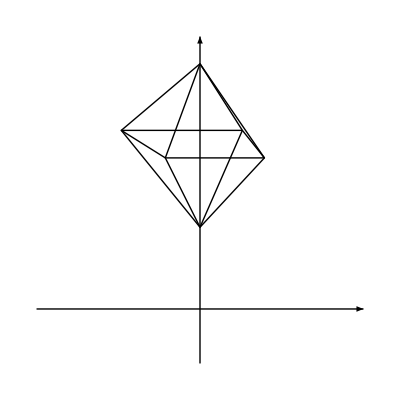

```mathematica
Graphics[{
Arrow[{{-3,0},{3,0}}],Arrow[{{0,-1},{0,5}}],
Line[{Delete[HomToOrth3D[A.PointA],1],Delete[HomToOrth3D[A.PointB],1],Delete[HomToOrth3D[A.PointC],1],Delete[HomToOrth3D[A.PointD],1],Delete[HomToOrth3D[A.PointA],1]}],
Line[{Delete[HomToOrth3D[A.PointA],1],Delete[HomToOrth3D[A.PointF],1],Delete[HomToOrth3D[A.PointC],1],Delete[HomToOrth3D[A.PointE],1],Delete[HomToOrth3D[A.PointA],1]}],
Line[{Delete[HomToOrth3D[A.PointF],1],Delete[HomToOrth3D[A.PointB],1],Delete[HomToOrth3D[A.PointE],1],Delete[HomToOrth3D[A.PointD],1],Delete[HomToOrth3D[A.PointF],1]}]
}]
```